```mathematica
ClearAll["Global`*"]
```

```mathematica
h=0.2;
```

```mathematica
u1[x_]:=x^2
```

```mathematica
(*read u_1*)
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_1_test.csv"];
t1=Table[{t1[[i,2]],t1[[i,1]]},{i,2,Length[t1]}]
```

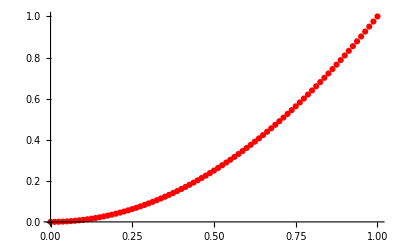

```mathematica
plotu1=ListPlot[t1,PlotStyle->Red]
```

```mathematica
plotu1on0=ParametricPlot3D[{t,h,u1[t]},{t,0,1},PlotStyle->Blue]
```

-Graphics3D-

```mathematica
(*read u_0*)
```

```mathematica
t0=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_0_test.csv"];
t0=Table[{t0[[i,2]],t0[[i,3]],t0[[i,1]]},{i,2,Length[t0]}]
```

```mathematica
plotu0=ListPointPlot3D[t0,PlotStyle->{Green,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[plotu0,plotu1on0]
```

-Graphics3D-